```mathematica
CLM=Import["~/Dropbox/TainoGroup/CLM_OMNI_EM_comparison.txt","TSV"];
PUR=Import["~/Dropbox/TainoGroup/PUR_OMNI_EM_comparison.txt","TSV"];
MXL=Import["~/Dropbox/TainoGroup/MXL_OMNI_EM_comparison.txt","TSV"];
```

```mathematica
CLM[[1]]
correction=100/99.; (*There was a rounding bug in the initial EM code, so estimated values must be scaled by this factor*)
```

{Chr,Pos,rsID,OMNI,CLM_low,CLM_est,CLM_high}

```mathematica
ratio[lin_]:=Module[{omni},omni=lin⟦4⟧;max=lin⟦7⟧*correction; If[omni> lin⟦6⟧*correction,(omni-lin⟦6⟧*correction)/(max-lin⟦6⟧*correction),(omni-lin⟦6⟧*correction)/-(lin⟦5⟧*correction-lin⟦6⟧*correction)]]
```

```mathematica
newdatsCLM=Map[ratio,CLM⟦2;;⟧];
newdatsPUR=Map[ratio,PUR⟦2;;⟧];
newdatsMXL=Map[ratio,MXL⟦2;;⟧];
```

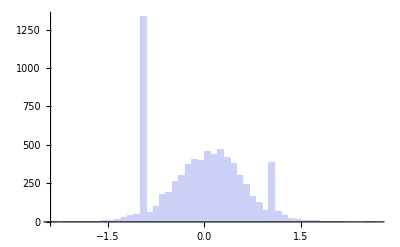

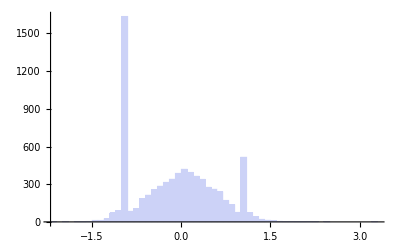

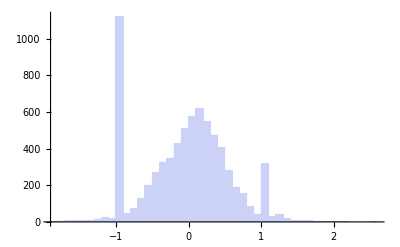

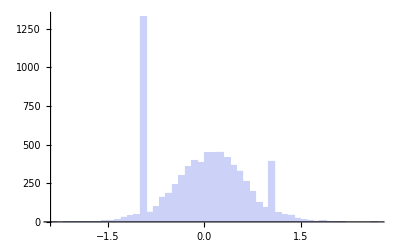

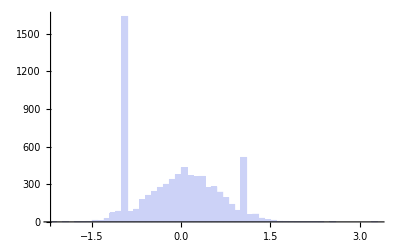

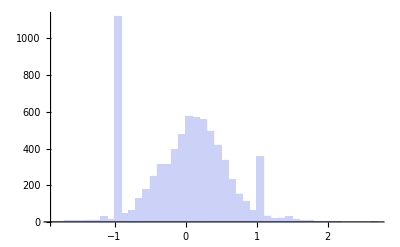

```mathematica
Histogram[newdatsCLM]
Histogram[newdatsPUR]
Histogram[newdatsMXL]
```

```mathematica
N[Length[Select[newdatsCLM,Abs[#]<=1.0001&]]/Length[newdatsCLM]]
N[Length[Select[newdatsPUR,Abs[#]<=1.0001&]]/Length[newdatsPUR]]
N[Length[Select[newdatsMXL,Abs[#]<=1.0001&]]/Length[newdatsMXL]]
```

0.94568

0.936824

0.968168

```mathematica
Max[MXL⟦2;;,7⟧]
```

0.99

```mathematica
MatrixForm[Pick[CLM⟦2;;⟧,Map[#>2&,newdatsCLM]]]
MatrixForm[Pick[CLM⟦2;;⟧,Map[#<-2&,newdatsCLM]]]
```

(15 | 94858889 | rs12101974 | 0.785714 | 0.21 | 0.385744 | 0.57
19 | 49244220 | rs2307019 | 0.769231 | 0.21 | 0.385035 | 0.57
19 | 55512137 | rs12768 | 1 | 0.14 | 0.346427 | 0.59
19 | 55686230 | rs2071572 | 0.708333 | 0.02 | 0.159005 | 0.37)

(19 | 44612231 | rs3746319 | 0.0555556 | 0.24 | 0.40594 | 0.59
19 | 54606405 | rs254259 | 0.037037 | 0.35 | 0.579616 | 0.79
19 | 55501834 | rs1654496 | 0 | 0.23 | 0.444424 | 0.66)

```mathematica
MatrixForm[Pick[MXL⟦2;;⟧,Map[#>2&,newdatsMXL]]]
MatrixForm[Pick[MXL⟦2;;⟧,Map[#<-1.7&,newdatsMXL]]]
```

(19 | 33605312 | rs10421769 | 1 | 0.63 | 0.769567 | 0.88
19 | 55512137 | rs12768 | 0.979167 | 0.57 | 0.716468 | 0.84
19 | 55686230 | rs2071572 | 0.645833 | 0.19 | 0.311423 | 0.44
19 | 55702910 | rs2288523 | 0.666667 | 0.25 | 0.383581 | 0.52
19 | 56459342 | rs306507 | 1 | 0.61 | 0.748156 | 0.87
19 | 57984918 | rs2074058 | 0.88 | 0.44 | 0.583899 | 0.72)

(9 | 138454301 | rs3748206 | 0.0188679 | 0.1 | 0.208637 | 0.34
15 | 68492028 | rs11071986 | 0.0555556 | 0.14 | 0.254268 | 0.39
19 | 33353464 | rs11084673 | 0 | 0.08 | 0.191324 | 0.32
19 | 33355055 | rs12150889 | 0 | 0.08 | 0.192915 | 0.32
19 | 40197924 | rs4830 | 0.136364 | 0.25 | 0.39085 | 0.54)

```mathematica
MatrixForm[Pick[PUR⟦2;;⟧,Map[#>2&,newdatsPUR]]]
MatrixForm[Pick[PUR⟦2;;⟧,Map[#<-1.7&,newdatsPUR]]]
```

(3 | 192994543 | rs2271791 | 1 | 0.03 | 0.253798 | 0.6
18 | 72176083 | rs2278161 | 0.692308 | 0 | 0.124827 | 0.38
19 | 36003721 | rs7254211 | 0.6 | 0.02 | 0.155083 | 0.37
19 | 49102513 | rs1052131 | 0.8125 | 0.11 | 0.303211 | 0.54
19 | 49438363 | rs2270941 | 0.705882 | 0 | 0.0770124 | 0.27
19 | 55686230 | rs2071572 | 0.833333 | 0 | 0.157487 | 0.45
19 | 57065189 | rs145011 | 0.5 | 0 | 0.0707379 | 0.26
19 | 57984918 | rs2074058 | 0.833333 | 0.02 | 0.182834 | 0.44)

(19 | 54606209 | rs254260 | 0.636364 | 0.8 | 0.942165 | 0.99
19 | 56423668 | rs304001 | 0.0833333 | 0.36 | 0.662648 | 0.9
19 | 56424443 | rs303997 | 0.0833333 | 0.36 | 0.656656 | 0.9
19 | 57036653 | rs3752176 | 0 | 0.39 | 0.786228 | 0.99
20 | 34560526 | rs11167280 | 0 | 0.23 | 0.520314 | 0.79)